```mathematica
Ggauss[q_, z_, r_] = Sum[PDF[PoissonDistribution[z],k]*k/z*Sum[PDF[BinomialDistribution[k-1,q],m]*CDF[NormalDistribution[r,0.2],m/k], {m, 0, k-1}],{k,1,100}];
```

```mathematica
Cascade2single[z_, r_] = (SeriesCoefficient[Series[Ggauss[q,  z, r], {q, 0,2}],1]-1)^2 - 4*(SeriesCoefficient[Series[Ggauss[q,  z, r], {q, 0,2}],0]*SeriesCoefficient[Series[Ggauss[q, z, r], {q, 0,2}],2]);
```

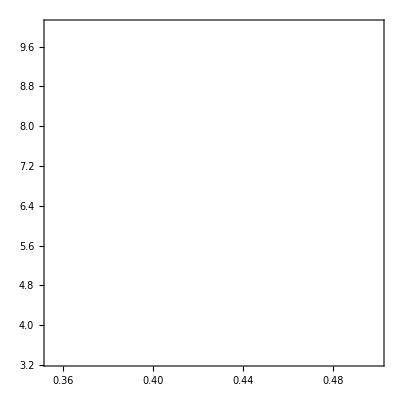

```mathematica
single = ContourPlot[(Cascade2single[z, r])==0, {r, 0.3543, 0.5}, {z,3.316,10}, ContourStyle->Directive[RGBColor[1.,1.,1.]]]
```

```mathematica
GE1gauss[q_, p_, z_, r_] = Sum[PDF[PoissonDistribution[z],k]*k/z*Sum[PDF[BinomialDistribution[k-1,q],m]*CDF[NormalDistribution[r,0.2],m/k], {m, 0, k-1}]*Sum[PDF[BinomialDistribution[k,p],w]*CDF[NormalDistribution[r,0.2],w/k], {w, 0, k}],{k,1,100}]
```

1/2 ⅇ^-z Erfc[3.53553 r] (1/2 p Erfc[3.53553 (-1+r)]+1/2 (1-p) Erfc[3.53553 r])+98+(ⅇ^-z 2 (1/2 q^99 Erfc[3.53553 (-99/100+r)]+98+1/2 1^99 Erfc[18 r]))/(93326215443944152681699238856266700490715968264381654979208272237582511852109168640000000000000000000000)
 |  |  |  |

```mathematica
CascadeEdge2[z_, r_] = (SeriesCoefficient[Series[GE1gauss[q, q, z, r], {q, 0,2}],1]-1)^2 - 4*(SeriesCoefficient[Series[GE1gauss[q, q, z, r], {q, 0,2}],0]*SeriesCoefficient[Series[GE1gauss[q, q, z, r], {q, 0,2}],2]);
```

```mathematica
Cascade4[z_, r_] = SeriesCoefficient[Series[GE1gauss[q, q, z, r], {q, 0,4}],4]
```

1/16 ⅇ^-z z^4 (10 Erfc[3.53553 (-2/5+r)]^2+10 Erfc[3.53553 (-3/5+r)] Erfc[3.53553 (-1/5+r)]-70 Erfc[3.53553 (-2/5+r)] Erfc[3.53553 (-1/5+r)]+7+21 Erfc[3.53553 r]^2)+96+1/2 ⅇ^1 1 (1/2 (Erfc[3.53553 (-1/3+r)]-Erfc[1]) (1)+3/4 1)
 |  |  |  |

```mathematica
deq[q_,z_, r_] = N[D[GE1gauss[q, q, z, r], {q, 1}]-1]
```

-1.+198+1.07151×10^-156 2.71828^(-1. z) z^99 (49.5 q^98 Erfc[1]+296) (0.5 q^100 Erfc[3.53553 (-1.+r)]+50. (1.-1. q) q^99 Erfc[3.53553 (-0.99+r)]+97+50. (1.-1. q)^99 q Erfc[3.53553 (-0.01+r)]+0.5 (1.-1. q)^100 Erfc[3.53553 r])
 |  |  |  |

```mathematica
ddeq[q_,z_, r_] = N[D[deq[q, z, r], {q, 1}]]
```

2.71828^(-1. z) z (0.5 Erfc[3.53553 (-0.5+r)]-0.5 Erfc[3.53553 r]) (q Erfc[3.53553 (-1.+r)]+(1.-1. q) Erfc[3.53553 (-0.5+r)]-1. q Erfc[3.53553 (-0.5+r)]-1. (1.-1. q) Erfc[3.53553 r])+296+1.07151×10^-156 3 (1)
 |  |  |  |

```mathematica
FindRoot[{GE1gauss[q, q, z, r] - q ==0,  deq[q, z, r] ==0, ddeq[q, z, r]==0}, {{q, 0}, {z, 1}, {r, 0.15}}]
```

{q→0.363303,z→1.71645,r→0.148895}

```mathematica
transline[z_] := N[FindRoot[{GE1gauss[q, q, z, r] == q,  deq[q, z, r] ==0}, {{q, 0}, {r, 0.2}}]][[2]]
```

```mathematica
transline[2]
```

r→0.161886

```mathematica
FindRoot[{GE1gauss[q,q,3.,0.2]==q,deq[q,3.,0.2]==0.},{q,0.}]
```

FindRoot::nveq: The number of equations does not match the number of variables in FindRoot[{GE1gauss[q,q,3.,0.2]==q,deq[q,3.,0.2]==0.},{q,0.}].

FindRoot[{GE1gauss[q,q,3.,0.2]==q,deq[q,3.,0.2]==0.},{q,0.}]

```mathematica
transline[3]
```

r→0.182524

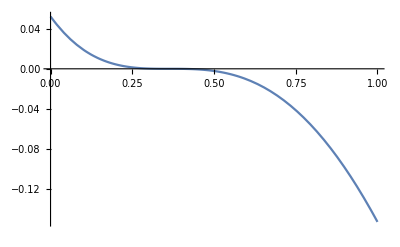

```mathematica
Plot[GE1gauss[q, q, 1.71645, 0.148895]-q, {q, 0, 1}]
```

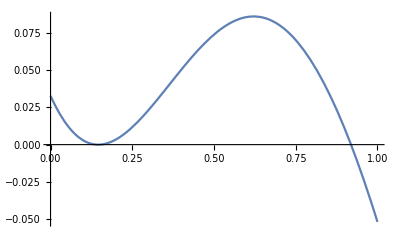

```mathematica
Plot[GE1gauss[q, q, 3, 0.182524]-q, {q, 0, 1}]
```

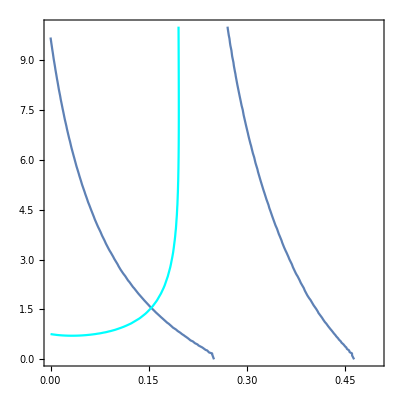

```mathematica
Show[%33, EdgeDouble]
```

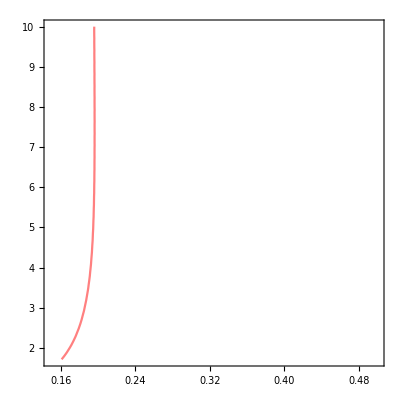

```mathematica
EdgeDouble = ContourPlot[(CascadeEdge2[z, r])==0 , {r, 0.1489, 0.5}, {z,1.71645,10}, ContourStyle->Directive[RGBColor[1,.5,0.5]]]
```

```mathematica
data=BinaryReadList["/home/user/Documents/BT_MP/BT_MP/coordination_game/simulations/pp_single_sim.dat","Real32"];
```

```mathematica
Length[data]
```

520

```mathematica
griddat = ArrayReshape[data, {20, 26}];
```

```mathematica
zcoord = Range[0.5, 10, 0.5];
```

```mathematica
Length[zcoord]
```

20

```mathematica
rcoord = Range[0, 0.5, 0.02];
```

```mathematica
Length[rcoord]
```

26

```mathematica
Surface= Flatten[Table[{rcoord[[j]],zcoord[[i]],griddat[[i,j]]},{j,26},{i,20}],1];
```

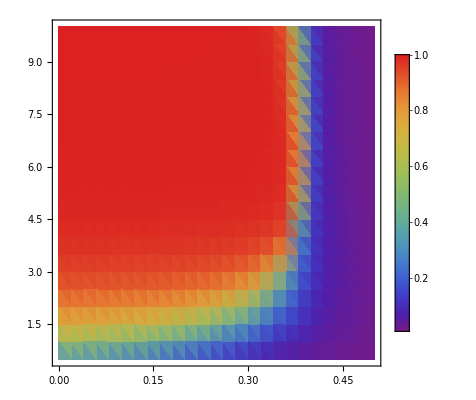

```mathematica
simulationdata = ListDensityPlot[Surface, ColorFunction->"Rainbow", PlotLegends->Automatic, ColorFunctionScaling->False]
```

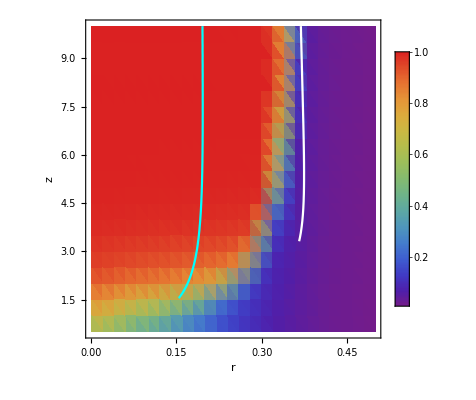

```mathematica
Finaldiagram = Show[simulationdata, single, EdgeDouble , FrameLabel->{{HoldForm[z],None},{HoldForm[r],None}},LabelStyle->{GrayLevel[0]}]
```

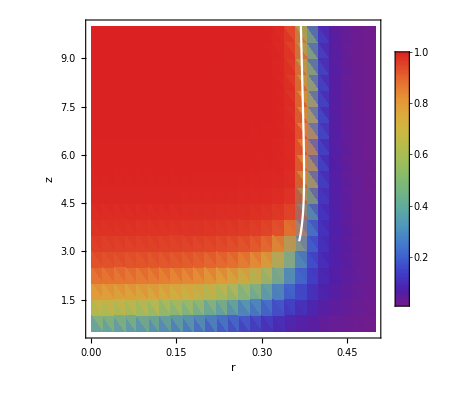

```mathematica
Finaldiagram = Show[simulationdata, single, FrameLabel->{{HoldForm[z],None},{HoldForm[r],None}},LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["~/Documents/BT_MP/BT_MP/MP_doc_templates/new_figs/pp_single.eps",Finaldiagram]
```

~/Documents/BT_MP/BT_MP/MP_doc_templates/new_figs/pp_single.eps

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["er_hetero_edge.eps"]]]
```